0.000236308+1.75588×10^-9 x

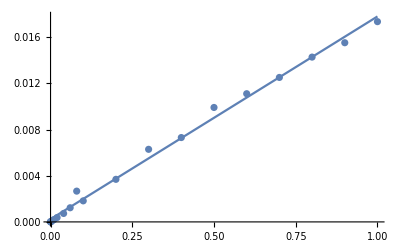

0.0000858628+1.46546×10^-9 x

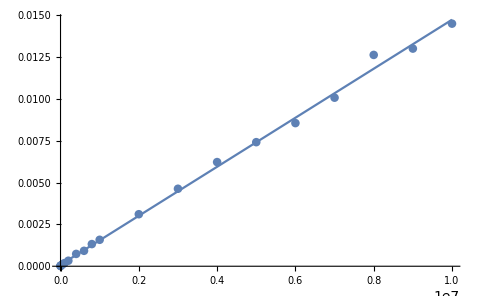

```mathematica
lineal=Fit[{{100,8.70228*10^-7},{1000,2.77758*10^-6},{5000,1.56999*10^-5},{10000,2.10762*10^-5},{50000,0.000100839},{100000,0.000190556},{200000,0.000375354},{400000,0.000731313},{600000,0.001224697},{800000,0.002665651},{1000000,0.001823199},{2000000,0.003687847},{3000000,0.006287658},{4000000,0.007306921},{5000000,0.009912563},{6000000,0.011102915},{7000000,0.012512947},{8000000,0.014274967},{9000000,0.015519405},{10000000,0.017345857}},{1,x},x]

puntosl=ListPlot[{{100,8.70228*10^-7},{1000,2.77758*10^-6},{5000,1.56999*10^-5},{10000,2.10762*10^-5},{50000,0.000100839},{100000,0.000190556},{200000,0.000375354},{400000,0.000731313},{600000,0.001224697},{800000,0.002665651},{1000000,0.001823199},{2000000,0.003687847},{3000000,0.006287658},{4000000,0.007306921},{5000000,0.009912563},{6000000,0.011102915},{7000000,0.012512947},{8000000,0.014274967},{9000000,0.015519405},{10000000,0.017345857}}]

g1=Plot[lineal,{x,0,10000000}]
Show[puntosl,g1,PlotRange->All]

linealhilos=Fit[{{100,1.91808*10^-5},{1000,2.19584*10^-5},{5000,3.016*10^-5},{10000,4.41432*10^-5},{50000,0.00011034},{100000,0.000185752},{200000,0.000329947},{400000,0.000737524},{600000,0.000922275},{800000,0.001324618},{1000000,0.001581335},{2000000,0.003110409},{3000000,0.004633558},{4000000,0.006227768},{5000000,0.007418943},{6000000,0.008559358},{7000000,0.010078263},{8000000,0.012636209},{9000000,0.013014209},{10000000,0.01450572}},{1,x},x]

puntoslh=ListPlot[{{100,1.91808*10^-5},{1000,2.19584*10^-5},{5000,3.016*10^-5},{10000,4.41432*10^-5},{50000,0.00011034},{100000,0.000185752},{200000,0.000329947},{400000,0.000737524},{600000,0.000922275},{800000,0.001324618},{1000000,0.001581335},{2000000,0.003110409},{3000000,0.004633558},{4000000,0.006227768},{5000000,0.007418943},{6000000,0.008559358},{7000000,0.010078263},{8000000,0.012636209},{9000000,0.013014209},{10000000,0.01450572}}]

g2=Plot[linealhilos,{x,0,10000000}]
Show[puntoslh,g2,PlotRange->All]
```